```mathematica
Quiet@Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
n=10;
data=Table[N[{x,Sin[x]}],{x,0,2Pi,(2Pi)/n}];
lpl=ListPlot[data,PlotStyle->{Red,PointSize[0.015]}];
iO=3;
int=Interpolation[data,InterpolationOrder->iO];
{xmin,xmax}=int[[1,1]];
Show[lpl,Plot[int[x],{x,xmin,xmax}],Plot[Sin[x],{x,xmin,xmax},PlotStyle->{Black,Dashed}]]
```

```mathematica
Plot[{int[x],Sin[x]},{x,xmin,3Pi}]
```

```mathematica
Options[Interpolation]
```

```mathematica
n=100;
data=Table[N[{x,Sin[x]}],{x,0,2Pi,(2Pi)/n}];
lpl=ListPlot[data,PlotStyle->{Red,PointSize[0.015]}];
iO=3;
int=Interpolation[data,InterpolationOrder->iO];
{xmin,xmax}=int[[1,1]];
Show[lpl,Plot[int[x],{x,xmin,xmax}],Plot[Sin[x],{x,xmin,xmax},PlotStyle->{Black,Dashed}]];
Plot[{int''[x],Sin''[x]},{x,xmin,xmax}];
```

```mathematica
Quiet@Remove["Global`*"];
n=100;
data=Flatten[Table[N[{x,y,Sin[x+2y]}],{x,0,2Pi,(2Pi)/n},{y,0,1Pi,(2Pi)/n}],1];
int=Interpolation[data];
{{xmin,xmax},{ymin,ymax}}=int[[1]];
(*Plot3D[Sin[x+2y]-int[x,y],{x,xmin,xmax},{y,ymin,ymax}]*)
int[[1]]
```

```mathematica
Part[int,1]
```

{{0.,6.28319},{0.,3.14159}}

```mathematica
expr=x+Sin[y^2+1]
```

x+Sin[1+y^2]

```mathematica
expr[[1]]=y
```

y

```mathematica
expr
```

y+Sin[1+y^2]

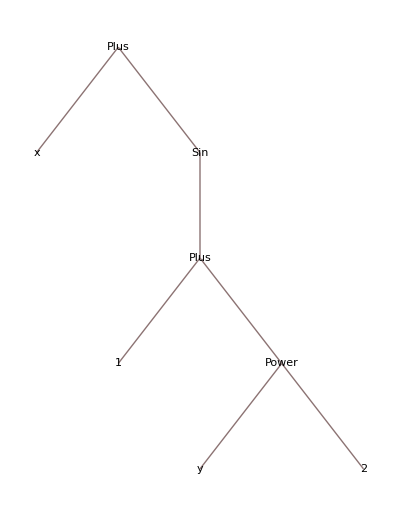

```mathematica
TreeForm[expr]
```

```mathematica
n=5;
data=Table[N[{x,Sin[x]}],{x,0,2Pi,(2Pi)/n}];
lpl=ListPlot[data,PlotStyle->{Red,PointSize[0.015]}];
iO=3;
int=Interpolation[data,InterpolationOrder->iO];
```

```mathematica
int[[1]]
```

{{0.,6.28319}}

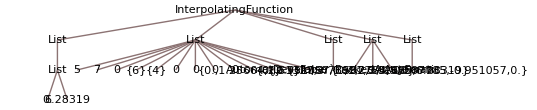

```mathematica
TreeForm[int]
```

```mathematica
list={1,2,{3,{romeo,juliet}}}
```

{1,2,{3,{romeo,juliet}}}

```mathematica
list[[3,2,2]]
```

juliet

```mathematica
FullForm[list]
```

List[1,2,List[3,List[romeo,juliet]]]

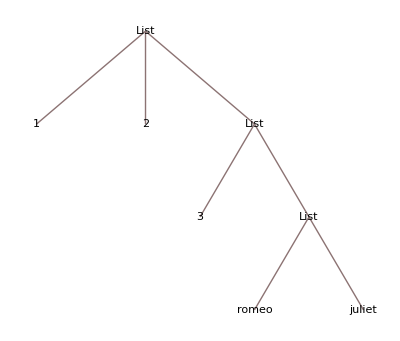

```mathematica
TreeForm[list]
```

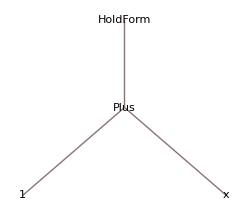

```mathematica
HoldForm[1+x]
```

```mathematica
expr=x+1+α+Subscript[k, 2]+Subscript[k, 1]
expr[[-1]]
```

1+x+α+k_1+k_2

k_2

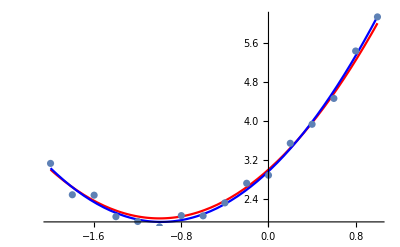

{2.96502+2.10526 x+1.06866 x^2,2.96502+2.10526 x+1.06866 x^2}

```mathematica
Quiet@Remove["Global`*"];
SeedRandom[1]
rn:=0.2*RandomReal[{-1,1}];
f[x_]:=1 x^2+2x+3;
data=Table[{x,f[x]+rn},{x,-2,1,0.2}];
ListPlot[data];
err[{x_,y_}]:=(y-(a*x^2+b*x+c))^2
totalError=Total[err/@data];
eqnsForCriticalPoints=0==D[totalError,#]&/@{a,b,c};
ruleForABC=Solve[eqnsForCriticalPoints][[1]];
y=a*x^2+b*x+c/.ruleForABC;
Show[Plot[{f[x],y},{x,-2,1},PlotStyle->{Red,Blue}],ListPlot[data]]
{Fit[data,{1,x,x^2},x],y}
```

```mathematica
Quiet@Remove["Global`*"];
f[t_]:=5+10*Exp[-4t];
data=Table[N[{t,f[t]}],{t,0,1,1/10}];
ListPlot[data];
FindFit[data,a+b*Exp[-c*t],{a,b,c},t]
```

{a→5.,b→10.,c→4.}

```mathematica
Quiet@Remove["Global`*"];
f[t_]:=5+10*t+3 t^2;
data=Table[N[{t,f[t]}],{t,0,1,1/10}];
ListPlot[data];
FindFit[data,a+b*t+c*t^2,{a,b,c},t]
a+b*t+c*t^2/.%
```

{a→5.,b→10.,c→3.}

5.+10. t+3. t^2